```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
mub={0,300,400,500,550,575,600};
fitdata=Table[Import["./mub"<>ToString[mub[[i]]]<>".dat"],{i,1,Length[mub]}];
```

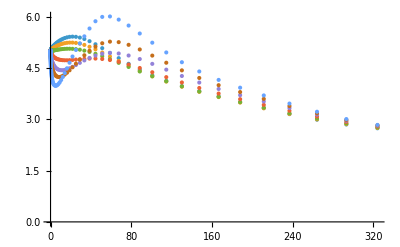

```mathematica
ListPlot[fitdata,PlotRange->All]
```

```mathematica
fitfun=Table[Interpolation[fitdata[[i]]],{i,1,Length[mub]}];
```

```mathematica
T=Table[Flatten[FindRoot[Abs[(fitfun[[i]][x]-5)/5]==0.01,{x,fitdata[[i]][[1]][[1]]}],2][[1]][[2]],{i,1,Length[mub]}]
Export["delta0p01.dat",%];
```

InterpolatingFunction::dmval: 输入值 {-0.00810081} 位于插值函数的数据范围之外. 将使用外推法.

{0.000186928,0.000112541,0.0000674165,0.25237,0.0481776,0.0000836538,0.000184088}

```mathematica
Table[Flatten[FindRoot[Abs[(fitfun[[i]][x]-5)/5]==0.03,{x,fitdata[[i]][[1]][[1]]}],2][[1]][[2]],{i,1,Length[mub]}]
Export["delta0p03.dat",%];
```

InterpolatingFunction::dmval: 输入值 {-0.00207295} 位于插值函数的数据范围之外. 将使用外推法.

InterpolatingFunction::dmval: 输入值 {-0.00284813} 位于插值函数的数据范围之外. 将使用外推法.

InterpolatingFunction::dmval: 输入值 {-0.00199173} 位于插值函数的数据范围之外. 将使用外推法.

General::stop: 在本次计算中，InterpolatingFunction::dmval 的进一步输出将被抑制.

{-0.0000433563,-0.000117247,-0.000166282,2.10064,0.357484,-0.00016449,-0.0000567525}

```mathematica
Table[Flatten[FindRoot[Abs[(fitfun[[i]][x]-5)/5]==0.05,{x,fitdata[[i]][[1]][[1]]}],2][[1]][[2]],{i,1,Length[mub]}]
Export["delta0p38.dat",%];
```

InterpolatingFunction::dmval: 输入值 {-0.00239254} 位于插值函数的数据范围之外. 将使用外推法.

InterpolatingFunction::dmval: 输入值 {-0.00380583} 位于插值函数的数据范围之外. 将使用外推法.

InterpolatingFunction::dmval: 输入值 {-0.00506069} 位于插值函数的数据范围之外. 将使用外推法.

General::stop: 在本次计算中，InterpolatingFunction::dmval 的进一步输出将被抑制.

{-0.000174119,-0.000252981,-0.000306683,7.69064,0.97686,-0.000312703,-0.000197368}

```mathematica
Export["mub2.dat",mub]
```

mub2.dat

```mathematica
mub2={0,100,200,300,400,500,550,575,600}
```

{0,100,200,300,400,500,550,575,600}

```mathematica
f=Interpolation[Transpose[{mub,T}],InterpolationOrder->1]
```

InterpolatingFunction[…]

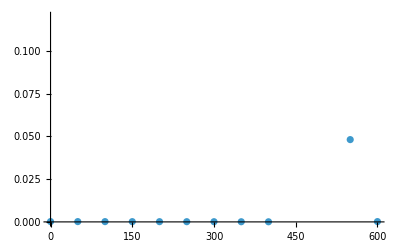

```mathematica
ListPlot[Table[{x,f[x]},{x,0,600,50}]]
```

```mathematica
Table[f[mub2[[i]]],{i,1,Length[mub2]}]
Export["delta0p01.dat",%];
```

{0.000186928,0.000162133,0.000137337,0.000112541,0.0000674165,0.25237,0.0481776,0.0000836538,0.000184088}